#### Valores experimentales de eritrocitos

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
datos0Im=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos2Im,datos1Im[[All,2]]}]];
parteRe=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]];
(*Se toma a la primera columna como el vector de energía*)
```

```mathematica
Export["parteIm.csv",Transpose[{energias,parteIm1}]]
```

parteIm.csv

```mathematica
Export["parteRe.csv",Transpose[{energias,parteRe1}]]
```

parteRe.csv

```mathematica
eps1[x_]:=parteRe[x]^2-parteIm[x]^2;
eps2[x_]:=(2*parteRe[x]*parteIm[x]);
```

```mathematica
parteIm1=Table[eps2[x],{x,1.19,4.82,0.01}];
parteRe1=Table[eps1[x],{x,1.19,4.82,0.01}];
energias=Range[1.19,4.82,0.01];
```

```mathematica
Max[parteIm1]
```

0.0319165

```mathematica
Export["parteIm.csv",Transpose[{energias,parteIm1}]]
```

parteIm.csv

```mathematica
Export["parteRe.csv",Transpose[{energias,parteRe1}]]
```

parteRe.csv

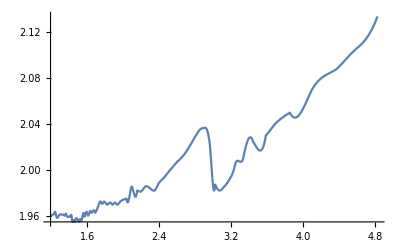

```mathematica
Plot[{eps1[x]},{x,1.19,4.83}]
```

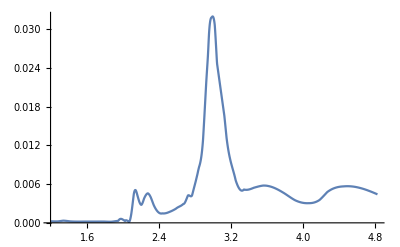

```mathematica
Plot[{eps2[x]},{x,1.19,4.83},PlotRange->All]
```

Ahora se van a ajustar las funciones con lorentzianas

InterpolatingFunction::dmval: Input value {4.83329} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84329} lies outside the range of data in the interpolating function. Extrapolation will be used.

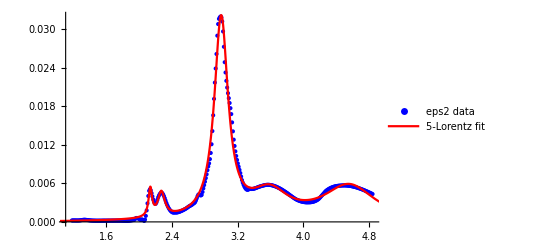

```mathematica
xmin=Min[datos2Im];
xmax=Max[datos2Im];

(* ==3. Datos para ajuste==*)
eps2Data=Table[{x,eps2[x]},{x,xmin,xmax,0.01}];

(* ==4. Definir suma de 5 Lorentzianas imaginarias==*)
lorentzSum[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=(A1 γ1 ω)/((ω01^2-ω^2)^2+(γ1 ω)^2)+(A2 γ2 ω)/((ω02^2-ω^2)^2+(γ2 ω)^2)+(A3 γ3 ω)/((ω03^2-ω^2)^2+(γ3 ω)^2)+(A4 γ4 ω)/((ω04^2-ω^2)^2+(γ4 ω)^2)+(A5 γ5 ω)/((ω05^2-ω^2)^2+(γ5 ω)^2);

(* ==5. Ajustar con NonlinearModelFit==*)
fit=NonlinearModelFit[eps2Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,2.15},{γ1,0.1},{A2,0.01},{ω02,2.3},{γ2,0.1},{A3,0.01},{ω03,3},{γ3,0.1},{A4,0.01},{ω04,3.6},{γ4,0.1},{A5,0.01},{ω05,4.5},{γ5,0.1}},ω];

(* ==6. Graficar datos originales y ajuste con 5 Lorentzianas==*)
Show[ListPlot[eps2Data,PlotStyle->Blue,PlotLegends->{"eps2 data"},PlotRange->All],Plot[fit[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"5-Lorentz fit"},PlotRange->All]]
```

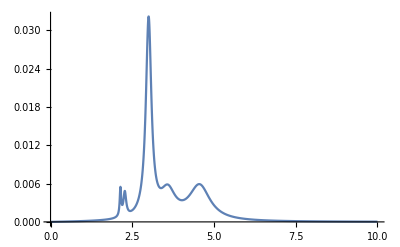

```mathematica
Plot[fit[ω],{ω,0,10},PlotRange->All]
```

```mathematica
eri=Table[fit[x],{x,0,10,0.01}];
omega=Range[0,10,0.01];
```

```mathematica
parteReKK1=kkrebook[omega,eri];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.13915×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

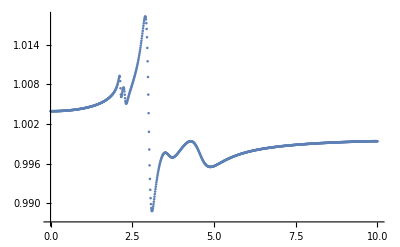

```mathematica
ListPlot[Transpose[{omega,parteReKK1}],PlotRange->All]
```

## Valores de 30.6 g/dL

```mathematica
{3,4}*{3,4}
```

{9,16}

```mathematica
datos0Im=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\30.6_uA_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos2Im=datos1Im[[All,1]];
datos3Im=datos1Im[[All,2]];
datos2Im=datos3Im*datos2Im*(10^(-6))/(4*Pi);
datos3Im=h c/datos1Im[[All,1]];

(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos3Im,datos2Im}]];
(*Se toma a la primera columna como el vector de energía*)
```